```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
TEMP = 9.*^-9; (* GeV *)
mn     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
vd  = 270.*^3;(* ms^-1 *)
vns =  200.*^3 ;(* ms^-1 *)
hbarc = (0.1973269788*1.*^-3); (* GeV fm *)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

```mathematica
avgμFn =NIntegrate[muFn[x]*x^2, {x,rMin, rMax}]/NIntegrate[x^2, {x, rMin, rMax}];
```

## Other Functions

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*NSMass[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*NSMass[rMax]*2.*^30)/(rMax*1.*^3)]/SOL
]; 


ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];
μ[mx_]:=mx/mn;
γ[r_]:= 1/Sqrt[1 - ve[r]^2]; (*natural units *)
p[r_, mx_]:=γ[r]*mx*ve[r];
s[r_,mx_] :=2γ[r]*mx*mn+mx^2+mn^2;(*mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√0.3)*μ[mx])*);
Er[ctheta_,r_, mx_]:= (mn*mx^2*γ[r]^2*ve[r]^2)/(mn^2 + mx^2 + 2*γ[r]*mx*mn)*(1 - ctheta);
jacobian[r_, mx_]:=1/(2*mn^2*p[0.6, mx]^2/s[r, mx])(*0.3*((1+μ[mx]^2+2/(√0.3)*μ[mx])/(2*(1-0.3)*mx^2))*);
σTot[dσ_,r_?NumericQ, mx_]:= NIntegrate[dσ[t,r,mx] ,{t,-4*mn^2*p[0.6, mx]^2/s[r, mx](*-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx])))*),0}]*jacobian[r, mx];
```

## Differential Cross Sections

```mathematica
d1[t_, r_, mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx]+1)^2*mx^2);
d2[t_, r_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[ mx]);
d3[t_, r_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, r_, mx_]:= (mn^2*t^2)/(32*π*s[r, mx]);
d5[t_, r_, mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[ mx]*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2))/(16*π*μ[mx]^4*s[ mx]);
d6[t_, r_, mx_]:= 1/(16*π*μ[mx]^4*s[r, mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[r, mx] +s[ mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2));
d7[t_, r_, mx_]:= 1/(16*π*μ[mx]^4*s[r, mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[r, mx] +s[r, mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[r, mx]^2+2*s[r, mx]*t+t^2));
d8[t_, r_, mx_]:= 1/(4*π*μ[mx]^4*s[r, mx])(2*(μ[mx]^4+10*μ[mx]^2+1)*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*mx^2*(s[r, mx]+t)+μ[mx]^4*(2*s[r, mx]^2+2*s[r, mx]*t+t^2));
d9[t_, r_, mx_]:= 1/(4*π*μ[mx]^4*s[r, mx])(4*(μ[mx]^4+4*μ[mx]^2+1)*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[r, mx]+t)+μ[mx]^4*(2*s[r, mx]+t)^2);
d10[t_, r_, mx_]:=1/(4*π*μ[mx]^4*s[r, mx])(4*(μ[mx]^2-1)^2*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[r, mx]+t)+μ[mx]^4*(2*s[r, mx]+t)^2);
```

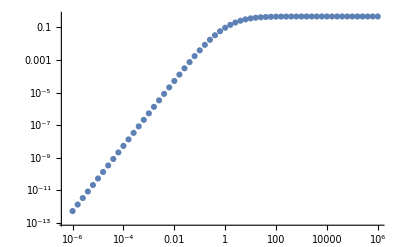

```mathematica
ListLogLogPlot[Evaluate@Table[ With[{x := 10^xp}, Table[{x,σTot[thing,11, x]}, {xp, -6, 6, 0.2}]], {thing, {d1}}]]
```

```mathematica
d1low[cθ_,w_, mx_]:= (mn^2*mx^2)/(2*π*(μ[mx]+1)^2);
d2low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d3low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d4low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(32*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2)^2;
d5low[cθ_,w_, mx_]:= mx^2/(2*π*(μ[mx]+1)^2);
```

```mathematica
(*ListLogLogPlot[With[{x:=10^xp}, Table[{x, Integrate[d5low[y, 0.6, x], {y, -1,1}]}, {xp, -6, 6, 0.2}]]]*)
```

## Average over angles

```mathematica
avgθ[dσ_,r_,mx_]:=NIntegrate[dσ[t,r,mx]*(-t)*(jacobian[r,mx])^2 ,{t,-4*mn^2*p[r, mx]^2/s[r, mx](*-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx])))*),0}]/NIntegrate[dσ[t,r,mx]*jacobian[r, mx] ,{t,-4*mn^2*p[r, mx]^2/s[r, mx](*-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx])))*),0}];
```

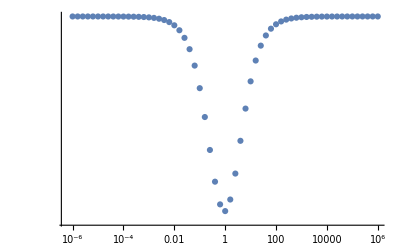

```mathematica
ListLogLogPlot[With[{x := 10^xp}, Table[{x,avgθ[d8,11, x]}, {xp, -6, 6, 0.2}]]]
```

```mathematica
qtr[dσ_, r_, mx_]:=√(2*mn*(mn*mx^2*γ[r]^2*ve[r]^2)/(mn^2 + mx^2 + 2*γ[r]*mx*mn)*avgθ[dσ,r, mx]);
```

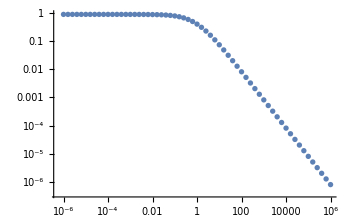

```mathematica
ListLogLogPlot[With[{x := 10^xp}, Table[{x,qtr[d4,11, x]/x}, {xp, -6, 6, 0.2}]]]
```

## Capture Rate

```mathematica
cap[dσ_,mx_]:=1/mx*NIntegrate[ve[r]^2*r^2*nd[r]*σTot[dσ, r, mx]*qtr[dσ, r, mx]/(√(2*mn*muFn[r]*1*^-3)), {r, rMin, rMax}];
```

```mathematica
cap[d1,mn]
```

6.67121

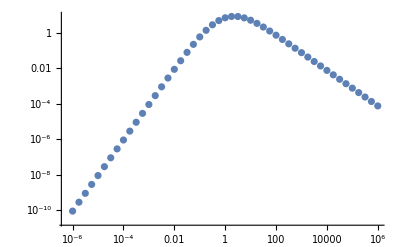

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x,cap[d1,x]}, {xp,-6,6, 0.25}]]]
```

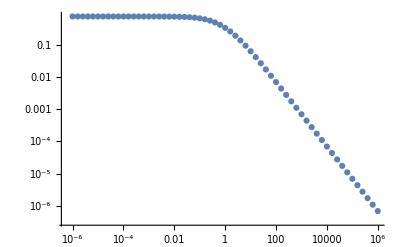

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x,1/x*qtr[d1, 11, x]}, {xp,-6,6, 0.2}]]]
```